# mTransport

## Transport method for non Slow-Roll dynmics and nontrivial field-space metrics

This is a code by written by Mafalda Dias, Jonathan Frazer and David Seery and we hope you find it useful. Any suggestions for improving the code, however minor, are greatly appreciated. Please contact us by email. 

Should you wish to refer to this code in a paper, please cite the corresponding paper arXiv: 1502.03125. 

This code was developed for Mathematica 9 and 10. Code last updated on June 2016. 

Copyright (c) 2015, Mafalda Dias, Jonathan Frazer and David Seery
All rights reserved.

Redistribution and use in source and binary forms, with or without modification, are permitted provided that the following conditions are met:

1. Redistributions of source code must retain the above copyright notice, this list of conditions and the following disclaimer.

2. Redistributions in binary form must reproduce the above copyright notice, this list of conditions and the following disclaimer in the documentation and/or other materials provided with the distribution.

3. Neither the name of the copyright holder nor the names of its contributors may be used to endorse or promote products derived from this software without specific prior written permission.

THIS SOFTWARE IS PROVIDED BY THE COPYRIGHT HOLDERS AND CONTRIBUTORS “AS IS” AND ANY EXPRESS OR IMPLIED WARRANTIES, INCLUDING, BUT NOT LIMITED TO, THE IMPLIED WARRANTIES OF MERCHANTABILITY AND FITNESS FOR A PARTICULAR PURPOSE ARE DISCLAIMED. IN NO EVENT SHALL THE COPYRIGHT HOLDER OR CONTRIBUTORS BE LIABLE FOR ANY DIRECT, INDIRECT, INCIDENTAL, SPECIAL, EXEMPLARY, OR CONSEQUENTIAL DAMAGES (INCLUDING, BUT NOT LIMITED TO, PROCUREMENT OF SUBSTITUTE GOODS OR SERVICES; LOSS OF USE, DATA, OR PROFITS; OR BUSINESS INTERRUPTION) HOWEVER CAUSED AND ON ANY THEORY OF LIABILITY, WHETHER IN CONTRACT, STRICT LIABILITY, OR TORT (INCLUDING NEGLIGENCE OR OTHERWISE) ARISING IN ANY WAY OUT OF THE USE OF THIS SOFTWARE, EVEN IF ADVISED OF THE POSSIBILITY OF SUCH DAMAGE.

## Launch parallel kernels

Terminate the kernels before rerunning the code. To use the command “Evaluate Notebook” from the menu, this first line must be commented out.

```mathematica
Quit[]
```

```mathematica
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
ParallelNeeds["DifferentialEquations`InterpolatingFunctionAnatomy`"];

LaunchKernels[]
$KernelCount
ParallelEvaluate[$ProcessID]
ParallelEvaluate[$MachineName]
```

{KernelObject[1,local],KernelObject[2,local]}

2

{4632,4636}

{chrobbie,chrobbie}

## Choose model and desired computations

### Control Panel

Change setting either by evaluating this cell a
nd then clicking on the checkbox output, dragging the sliders etc, or alternatively by changing the default settings directly.

```mathematica
(*Default settings*)
model=4;
NexittoNend=55;
Nsubhorizon=6;
ComputensTransport=True;
ComputensFiniteDifference=True;
ComputePofk=True;
Nrange=4;
ksteps=200;

Grid[{
{"Model number",PopupMenu[Dynamic@model,{1,2,3,4,5}]} ,
{"Set pivot scale (N_end-N_exit)",Slider[Dynamic@NexittoNend,{0,60,1}], Dynamic@NexittoNend},
{"Set the number of e-folds of subhorizon evolution",Slider[Dynamic@Nsubhorizon,{0,15,1}], Dynamic@Nsubhorizon},
{"Compute n_s using n_abtransport equation",Checkbox@Dynamic@ComputensTransport},
{"Compute n_s using using finite difference",Checkbox@Dynamic@ComputensFiniteDifference},
{"Compute full powerspectum P_ζ(k)", Checkbox@Dynamic@ComputePofk},
{"Set the range of scales (in e-folds) over which P_ζ(k)is computed",
Slider[Dynamic@Nrange,{2,Dynamic@NexittoNend,0.5}], Dynamic@Nrange},
{"Set the number of points computed to construct P_ζ(k)",Slider[Dynamic@ksteps,{10,300,10}], Dynamic@ksteps},
{"Click here to evaluate the rest of the code",Button["Evaluate",SelectionMove[EvaluationNotebook[],Next,CellGroup];
SelectionEvaluate[EvaluationNotebook[]]]}
}]
```

Model number |  | 
Set pivot scale (N_end-N_exit) |  | 
Set the number of e-folds of subhorizon evolution |  | 
Compute n_s using n_abtransport equation |  | 
Compute n_s using using finite difference |  | 
Compute full powerspectum P_ζ(k) |  | 
Set the range of scales (in e-folds) over which P_ζ(k)is computed |  | 
Set the number of points computed to construct P_ζ(k) |  | 
Click here to evaluate the rest of the code | Evaluate |

## Fields, potential and metric

### Model List

A new model can easily be added by continuing the Which statement. If it is not immediately clear how to do so, please click on the link below to see the Documentation. Note that in order for the code to be reliable, the potential needs to be normalised such as to give sensible values for the amplitude of the power spectrum. If the fluctuations are so large that perturbation theory does not hold, then the code may not run succcessfully (e.g errors such as NDSolve::ndsz may occur).

```mathematica
Hyperlink["Which Documentation","paclet:ref/Which"]
```

Which Documentationpaclet:ref/Which

(γ = G_αβ,  γinv=G^αβ).

```mathematica
Which[
model==1,

d=2;(*This sets the field-space dimension and is crucial for constructing all equations*)
ϕα=Table[Symbol["ϕ"<>ToString[i]][t],{i,d}];
ϕinitial=√((4*61)/d)ConstantArray[1,d];
πinitial=ConstantArray[0,d];
γ=IdentityMatrix[d];
M=10^-5;
m2α=M^2 Range[d]^2;
V=1/2 m2α.ϕα^2;
,

model==2,
d=3;(*This sets the field-space dimension and is crucial for constructing all equations*)
ϕinitial={10,0.01,13};
πinitial={0,0,0};

γ={{1,Γ,0},{Γ,1,0},{0,0,1}};
Γ=Γ0/Cosh[2(ϕ1[t]-7)/Δχ]^2;
V=1/2 300 M^2 ϕ2[t]^2+1/2 30 M^2 ϕ1[t]^2+1/2 30/81 M^2 ϕ3[t]^2;
M=10^-6;
Δχ=0.12;
Γ0=0.9;

,

model==3,
d=1;(*This sets the field-space dimension and is crucial for constructing all equations*)
ϕα=Table[Symbol["ϕ"<>ToString[i]][t],{i,d}];
ϕinitial={18};
πinitial=ConstantArray[0,d];
γ=IdentityMatrix[d];
M=10^-5;
m2α=M^2 Range[d]^2;
V=1/2 m2α.ϕα^2;
,
model==4,
d=5;(*This sets the field-space dimension and is crucial for constructing all equations*)
ϕα=Table[Symbol["ϕ"<>ToString[i]][t],{i,d}];
ϕinitial={15,10,-5,10,3};
πinitial=ConstantArray[0,d];
γ=IdentityMatrix[d];
m2α=10^#&/@{-10,-10,-9,-10,-8};
V=1/2 m2α.ϕα^2;

]
```

```mathematica
{V,N@ϕinitial}
```

{1/2 (ϕ1[t]^2/10000000000+ϕ2[t]^2/10000000000+ϕ3[t]^2/1000000000+ϕ4[t]^2/10000000000+ϕ5[t]^2/100000000),{15.,10.,-5.,10.,3.}}

### Fields and metric definitions

d=N_f. Greek indices run through N_f and Latin indices run through 2N_f.
To avoid confusion between a and b in the labeling of each element of Σab and nab, which would happen for N_f>10, these labels are separated by “o”.

```mathematica
ϕα=Table[Symbol["ϕ"<>ToString[i]][t],{i,d}];
πα=Table[Symbol["π"<>ToString[i]][t],{i,d}];

Σab=Table[Which[
j≥i,Symbol["Σ"<>ToString[i]<>"o"<>ToString[j]][t],
j<i,Symbol["Σ"<>ToString[j]<>"o"<>ToString[i]][t]
],{i,2d},{j,2d}];

nab=Table[Which[
j≥i,Symbol["n"<>ToString[i]<>"o"<>ToString[j]][t],
j<i,Symbol["n"<>ToString[j]<>"o"<>ToString[i]][t]
],{i,2d},{j,2d}];

Γab=Table[Which[
j≥i,Symbol["Γ"<>ToString[i]<>ToString[j]][t],
j<i,Symbol["Γ"<>ToString[j]<>ToString[i]][t]
],{i,2},{j,2}];

nTab=Table[Which[
j≥i,Symbol["nT"<>ToString[i]<>ToString[j]][t],
j<i,Symbol["nT"<>ToString[j]<>ToString[i]][t]
],{i,2},{j,2}];
```

We set k -- the pivot comoving scale at which we evaluate our parameters -- to be the scale that crossed the horizon at Nexit, i.e. NexittoNend e-folds before the end of inflation. 
Nstart is the beginning of the evaluation of the perturbations, i.e. NexittoNend+Nsubhorizon e-folds before the end of inflation.

```mathematica
Ninitial=0;
k=ⅇ^Nexit Hexit;
```

Compute Christoffel symbols (Γ^a)_bc

```mathematica
γinv=Inverse[γ];
h=Simplify[Table[1/2 Sum[γinv[[i,m]](D[γ[[m,k]],ϕα[[j]]]+D[γ[[j,m]],ϕα[[k]]]-D[γ[[j,k]],ϕα[[m]]]),{m,d}],{i,d},{j,d},{k,d}]];
```

Compute Riemann tensor  in the form (R^a)_bcd

```mathematica
Riemann=Simplify[Table[D[h[[a,b,c]],ϕα[[f]]]-D[h[[a,b,f]],ϕα[[c]]]+Sum[h[[m,b,c]]h[[a,f,m]],{m,d}]-Sum[h[[m,b,f]]h[[a,c,m]],{m,d}],{a,d},{b,d},{f,d},{c,d}]];
```

## Field derivatives, velocities, expansion tensors, etc.

```mathematica
ϵ=1/2 πα.γ.πα;
H=√(V/(3-ϵ));
```

### Compute derivatives V^α, (V^α)_β

CovariantVα=V_(; α) , Vα=V^(; α), CovariantVαβ = V_(; αβ) , Vαβ=(V^(; α))_β.

```mathematica
CovariantVα=Map[D[V,#]&,ϕα];
CovariantVαβ=Table[D[CovariantVα[[i]],ϕα[[j]]]-Sum[h[[m,i,j]]CovariantVα[[m]],{m,d}],{i,d},{j,d}];
Vα=Table[Sum[γinv[[i,m]]CovariantVα[[m]],{m,d}],{i,d}];
Vαβ=Table[D[Vα[[i]],ϕα[[j]]]+Sum[h[[i,j,m]]Vα[[m]],{m,d}],{i,d},{j,d}];
```

```mathematica
Covariantvα=-D[V,{ϕα}]/(3 H^2);
vα=γinv.Covariantvα;
vαβ=D[vα,{ϕα}]+h.vα;
```

### Mass Matrix

```mathematica
mαβ=Table[
Sum[γinv[[ω,α]](CovariantVαβ[[α,β]]
-H^2 Sum[γ[[α,μ]]Riemann[[μ,l,δ,β]]πα[[l]]πα[[δ]],{l,d},{δ,d},{μ,d}]
-H^2(3+ϵ)Sum[γ[[α,μ]]πα[[μ]],{μ,d}]Sum[γ[[β,ν]]πα[[ν]],{ν,d}]
+2 H^2 ϵ Sum[γ[[β,ν]]πα[[ν]],{ν,d}]Sum[γ[[α,μ]]πα[[μ]],{μ,d}]
-H^2 Sum[γ[[α,μ]]πα[[μ]],{μ,d}]Sum[γ[[β,ν]](3vα[[ν]]+3(ϵ/3-1)πα[[ν]]),{ν,d}]
-H^2 Sum[γ[[β,μ]]πα[[μ]],{μ,d}]Sum[γ[[α,ν]](3vα[[ν]]+3(ϵ/3-1)πα[[ν]]),{ν,d}])
,{α,d}]
,{ω,d},{β,d}];
```

```mathematica
Simplify@mαβ
```

{{(2+4 π1[t] ϕ1[t]+π1[t]^2 (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2))/20000000000,(2 π1[t] ϕ2[t]+π2[t] (2 ϕ1[t]+π1[t] ϕ1[t]^2+π1[t] (ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/20000000000,(20 π1[t] ϕ3[t]+π3[t] (2 ϕ1[t]+π1[t] ϕ1[t]^2+π1[t] (ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/20000000000,(2 π1[t] ϕ4[t]+π4[t] (2 ϕ1[t]+π1[t] ϕ1[t]^2+π1[t] (ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/20000000000,(200 π1[t] ϕ5[t]+π5[t] (2 ϕ1[t]+π1[t] ϕ1[t]^2+π1[t] (ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/20000000000},{(2 π1[t] ϕ2[t]+π2[t] (2 ϕ1[t]+π1[t] ϕ1[t]^2+π1[t] (ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/20000000000,(2+4 π2[t] ϕ2[t]+π2[t]^2 (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2))/20000000000,(2 π3[t] ϕ2[t]+π2[t] (20 ϕ3[t]+π3[t] (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/20000000000,(2 π4[t] ϕ2[t]+π2[t] (2 ϕ4[t]+π4[t] (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/20000000000,(2 π5[t] ϕ2[t]+π2[t] (200 ϕ5[t]+π5[t] (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/20000000000},{(20 π1[t] ϕ3[t]+π3[t] (2 ϕ1[t]+π1[t] ϕ1[t]^2+π1[t] (ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/20000000000,(2 π3[t] ϕ2[t]+π2[t] (20 ϕ3[t]+π3[t] (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/20000000000,(20+40 π3[t] ϕ3[t]+π3[t]^2 (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2))/20000000000,(20 π4[t] ϕ3[t]+π3[t] (2 ϕ4[t]+π4[t] (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/20000000000,(20 π5[t] ϕ3[t]+π3[t] (200 ϕ5[t]+π5[t] (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/20000000000},{(2 π1[t] ϕ4[t]+π4[t] (2 ϕ1[t]+π1[t] ϕ1[t]^2+π1[t] (ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/20000000000,(2 π4[t] ϕ2[t]+π2[t] (2 ϕ4[t]+π4[t] (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/20000000000,(20 π4[t] ϕ3[t]+π3[t] (2 ϕ4[t]+π4[t] (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/20000000000,(2+4 π4[t] ϕ4[t]+π4[t]^2 (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2))/20000000000,(2 π5[t] ϕ4[t]+π4[t] (200 ϕ5[t]+π5[t] (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/20000000000},{(200 π1[t] ϕ5[t]+π5[t] (2 ϕ1[t]+π1[t] ϕ1[t]^2+π1[t] (ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/20000000000,(2 π5[t] ϕ2[t]+π2[t] (200 ϕ5[t]+π5[t] (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/20000000000,(20 π5[t] ϕ3[t]+π3[t] (200 ϕ5[t]+π5[t] (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/20000000000,(2 π5[t] ϕ4[t]+π4[t] (200 ϕ5[t]+π5[t] (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/20000000000,(200+400 π5[t] ϕ5[t]+π5[t]^2 (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2))/20000000000}}

```mathematica
Simplify[m2α-H^2 Outer[Times,πα,πα](3+ϵ)-(Outer[Times,πα,-(3 H^2 πα+Vα)]+Outer[Times,-(3 H^2 πα+Vα),πα])]
```

{{(2+4 π1[t] ϕ1[t]+π1[t]^2 (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2))/20000000000,(2+2 π1[t] ϕ2[t]+π2[t] (2 ϕ1[t]+π1[t] ϕ1[t]^2+π1[t] (ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/20000000000,(2+20 π1[t] ϕ3[t]+π3[t] (2 ϕ1[t]+π1[t] ϕ1[t]^2+π1[t] (ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/20000000000,(2+2 π1[t] ϕ4[t]+π4[t] (2 ϕ1[t]+π1[t] ϕ1[t]^2+π1[t] (ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/20000000000,(2+200 π1[t] ϕ5[t]+π5[t] (2 ϕ1[t]+π1[t] ϕ1[t]^2+π1[t] (ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/20000000000},{(2+2 π1[t] ϕ2[t]+π2[t] (2 ϕ1[t]+π1[t] ϕ1[t]^2+π1[t] (ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/20000000000,(2+4 π2[t] ϕ2[t]+π2[t]^2 (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2))/20000000000,(2+2 π3[t] ϕ2[t]+π2[t] (20 ϕ3[t]+π3[t] (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/20000000000,(2+2 π4[t] ϕ2[t]+π2[t] (2 ϕ4[t]+π4[t] (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/20000000000,(2+2 π5[t] ϕ2[t]+π2[t] (200 ϕ5[t]+π5[t] (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/20000000000},{(20 (1+π1[t] ϕ3[t])+π3[t] (2 ϕ1[t]+π1[t] ϕ1[t]^2+π1[t] (ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/20000000000,(20+2 π3[t] ϕ2[t]+π2[t] (20 ϕ3[t]+π3[t] (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/20000000000,(20+40 π3[t] ϕ3[t]+π3[t]^2 (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2))/20000000000,(20 (1+π4[t] ϕ3[t])+π3[t] (2 ϕ4[t]+π4[t] (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/20000000000,(20 (1+π5[t] ϕ3[t])+π3[t] (200 ϕ5[t]+π5[t] (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/20000000000},{(2+2 π1[t] ϕ4[t]+π4[t] (2 ϕ1[t]+π1[t] ϕ1[t]^2+π1[t] (ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/20000000000,(2+2 π4[t] ϕ2[t]+π2[t] (2 ϕ4[t]+π4[t] (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/20000000000,(2+20 π4[t] ϕ3[t]+π3[t] (2 ϕ4[t]+π4[t] (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/20000000000,(2+4 π4[t] ϕ4[t]+π4[t]^2 (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2))/20000000000,(2+2 π5[t] ϕ4[t]+π4[t] (200 ϕ5[t]+π5[t] (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/20000000000},{(200 (1+π1[t] ϕ5[t])+π5[t] (2 ϕ1[t]+π1[t] ϕ1[t]^2+π1[t] (ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/20000000000,(200+2 π5[t] ϕ2[t]+π2[t] (200 ϕ5[t]+π5[t] (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/20000000000,(20 (10+π5[t] ϕ3[t])+π3[t] (200 ϕ5[t]+π5[t] (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/20000000000,(200+2 π5[t] ϕ4[t]+π4[t] (200 ϕ5[t]+π5[t] (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/20000000000,(200+400 π5[t] ϕ5[t]+π5[t]^2 (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2))/20000000000}}

### Compute expansion tensors and constituents

Slow-Roll expansion tensor

```mathematica
uαβSR=Table[vαβ[[i,j]]-1/3 Sum[Riemann[[i,m,j,n]]vα[[m]]vα[[n]],{m,d},{n,d}],{i,d},{j,d}];
```

Expansion tensor (u^a)_b

```mathematica
kαβ=-k^2 IdentityMatrix[d]/(ⅇ^(2t)H^2);
```

```mathematica
ubarαβ=-mαβ/H^2+kαβ;
ubarαbarβ=IdentityMatrix[d](ϵ-3);
```

```mathematica
uab=Join[Join[Table[0,{i,d},{j,d}],IdentityMatrix[d],2],Join[ubarαβ,ubarαbarβ,2]];
```

```mathematica
Simplify@uab
```

{{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1},{(ⅇ^(-2 t) (-6+π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2) (2 (ⅇ^(2 t)+10000000000 ⅇ^(2 Nexit) Hexit^2)+4 ⅇ^(2 t) π1[t] ϕ1[t]+ⅇ^(2 t) π1[t]^2 (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/(2 (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)),((-6+π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2) (2 π1[t] ϕ2[t]+π2[t] (2 ϕ1[t]+π1[t] ϕ1[t]^2+π1[t] (ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2))))/(2 (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)),((-6+π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2) (20 π1[t] ϕ3[t]+π3[t] (2 ϕ1[t]+π1[t] ϕ1[t]^2+π1[t] (ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2))))/(2 (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)),((-6+π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2) (2 π1[t] ϕ4[t]+π4[t] (2 ϕ1[t]+π1[t] ϕ1[t]^2+π1[t] (ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2))))/(2 (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)),((-6+π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2) (200 π1[t] ϕ5[t]+π5[t] (2 ϕ1[t]+π1[t] ϕ1[t]^2+π1[t] (ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2))))/(2 (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)),1/2 (-6+π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2),0,0,0,0},{((-6+π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2) (2 π1[t] ϕ2[t]+π2[t] (2 ϕ1[t]+π1[t] ϕ1[t]^2+π1[t] (ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2))))/(2 (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)),(ⅇ^(-2 t) (-6+π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2) (2 (ⅇ^(2 t)+10000000000 ⅇ^(2 Nexit) Hexit^2)+4 ⅇ^(2 t) π2[t] ϕ2[t]+ⅇ^(2 t) π2[t]^2 (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/(2 (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)),((-6+π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2) (2 π3[t] ϕ2[t]+π2[t] (20 ϕ3[t]+π3[t] (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2))))/(2 (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)),((-6+π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2) (2 π4[t] ϕ2[t]+π2[t] (2 ϕ4[t]+π4[t] (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2))))/(2 (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)),((-6+π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2) (2 π5[t] ϕ2[t]+π2[t] (200 ϕ5[t]+π5[t] (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2))))/(2 (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)),0,1/2 (-6+π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2),0,0,0},{((-6+π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2) (20 π1[t] ϕ3[t]+π3[t] (2 ϕ1[t]+π1[t] ϕ1[t]^2+π1[t] (ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2))))/(2 (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)),((-6+π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2) (2 π3[t] ϕ2[t]+π2[t] (20 ϕ3[t]+π3[t] (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2))))/(2 (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)),(ⅇ^(-2 t) (-6+π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2) (20 (ⅇ^(2 t)+1000000000 ⅇ^(2 Nexit) Hexit^2)+40 ⅇ^(2 t) π3[t] ϕ3[t]+ⅇ^(2 t) π3[t]^2 (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/(2 (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)),((-6+π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2) (20 π4[t] ϕ3[t]+π3[t] (2 ϕ4[t]+π4[t] (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2))))/(2 (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)),((-6+π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2) (20 π5[t] ϕ3[t]+π3[t] (200 ϕ5[t]+π5[t] (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2))))/(2 (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)),0,0,1/2 (-6+π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2),0,0},{((-6+π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2) (2 π1[t] ϕ4[t]+π4[t] (2 ϕ1[t]+π1[t] ϕ1[t]^2+π1[t] (ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2))))/(2 (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)),((-6+π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2) (2 π4[t] ϕ2[t]+π2[t] (2 ϕ4[t]+π4[t] (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2))))/(2 (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)),((-6+π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2) (20 π4[t] ϕ3[t]+π3[t] (2 ϕ4[t]+π4[t] (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2))))/(2 (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)),(ⅇ^(-2 t) (-6+π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2) (2 (ⅇ^(2 t)+10000000000 ⅇ^(2 Nexit) Hexit^2)+4 ⅇ^(2 t) π4[t] ϕ4[t]+ⅇ^(2 t) π4[t]^2 (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/(2 (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)),((-6+π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2) (2 π5[t] ϕ4[t]+π4[t] (200 ϕ5[t]+π5[t] (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2))))/(2 (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)),0,0,0,1/2 (-6+π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2),0},{((-6+π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2) (200 π1[t] ϕ5[t]+π5[t] (2 ϕ1[t]+π1[t] ϕ1[t]^2+π1[t] (ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2))))/(2 (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)),((-6+π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2) (2 π5[t] ϕ2[t]+π2[t] (200 ϕ5[t]+π5[t] (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2))))/(2 (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)),((-6+π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2) (20 π5[t] ϕ3[t]+π3[t] (200 ϕ5[t]+π5[t] (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2))))/(2 (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)),((-6+π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2) (2 π5[t] ϕ4[t]+π4[t] (200 ϕ5[t]+π5[t] (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2))))/(2 (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)),(ⅇ^(-2 t) (-6+π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2) (200 (ⅇ^(2 t)+100000000 ⅇ^(2 Nexit) Hexit^2)+400 ⅇ^(2 t) π5[t] ϕ5[t]+ⅇ^(2 t) π5[t]^2 (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)))/(2 (ϕ1[t]^2+ϕ2[t]^2+10 ϕ3[t]^2+ϕ4[t]^2+100 ϕ5[t]^2)),0,0,0,0,1/2 (-6+π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)}}

Expansion tensor for tensor modes

```mathematica
wbar=-k^2/(ⅇ^(2t)H^2);
wbarbar=(ϵ-3);
wab=Join[{{0,1}},{{wbar,wbarbar}}];
```

## Transport equations of correlation functions

### Transport equations

Background

```mathematica
ϕeq=Table[D[ϕα[[i]],t]==πα[[i]],{i,d}];
πeq=Table[D[πα[[i]],t]+Sum[h[[i,m,n]]πα[[m]]πα[[n]],{m,d},{n,d}]==3vα[[i]]+3(ϵ/3-1)πα[[i]],{i,d}];
```

2pf

```mathematica
Σeq=DeleteCases[Flatten[Table[If[j≥i,
D[Σab[[i,j]],t]
+If[i≤d,Sum[h[[i,m,n]]Σab[[m,j]]πα[[n]],{m,d},{n,d}],Sum[h[[i-d,m,n]]Σab[[m+d,j]]πα[[n]],{m,d},{n,d}]]
+If[j≤d,Sum[h[[j,m,n]]Σab[[i,m]]πα[[n]],{m,d},{n,d}],Sum[h[[j-d,m,n]]Σab[[i,m+d]]πα[[n]],{m,d},{n,d}]]
==Sum[uab[[i,k]]Σab[[k,j]]+uab[[j,k]]Σab[[i,k]],{k,2d}],REMOVE],{i,2d},{j,2d}]],REMOVE];
```

Scale dependence of 2pf

```mathematica
kderiv=Join[Join[Table[0,{i,d},{j,d}],Table[0,{i,d},{j,d}],2],Join[Table[(2 k^2)/(ⅇ^(2t)H^2)KroneckerDelta[i,j],{i,d},{j,d}],Table[0,{i,d},{j,d}],2]];
```

```mathematica
neq=DeleteCases[Flatten[Table[If[j≥i,
D[nab[[i,j]],t]
+If[i≤d,Sum[h[[i,m,n]]nab[[m,j]]πα[[n]],{m,d},{n,d}],Sum[h[[i-d,m,n]]nab[[m+d,j]]πα[[n]],{m,d},{n,d}]]
+If[j≤d,Sum[h[[j,m,n]]nab[[i,m]]πα[[n]],{m,d},{n,d}],Sum[h[[j-d,m,n]]nab[[i,m+d]]πα[[n]],{m,d},{n,d}]]
==Sum[uab[[i,k]]nab[[k,j]]+uab[[j,k]]nab[[k,i]]-kderiv[[i,k]]Σab[[k,j]]-kderiv[[j,k]]Σab[[k,i]],{k,2d}],REMOVE],{i,2d},{j,2d}]],REMOVE];
```

Tensors 2pf

```mathematica
Γeq=DeleteCases[Flatten[Table[If[j≥i,
D[Γab[[i,j]],t]
==Sum[wab[[i,k]]Γab[[k,j]]+wab[[j,k]]Γab[[i,k]],{k,2}],REMOVE],{i,2},{j,2}]],REMOVE];
```

Scale dependence of tensors 2pf

```mathematica
kTderiv=Join[{{0,0}},{{(2 k^2)/(ⅇ^(2t)H^2),0}}] ;
```

```mathematica
nTeq=DeleteCases[Flatten[Table[If[j≥i,
D[nTab[[i,j]],t]
==Sum[wab[[i,k]]nTab[[k,j]]+wab[[j,k]]nTab[[i,k]]-kTderiv[[i,k]]Γab[[k,j]]-kTderiv[[j,k]]Γab[[k,i]],{k,2}],REMOVE],{i,2},{j,2}]],REMOVE];
```

## Solving the transport system

### Initial conditions

Initial conditions for background at Ninitial.

```mathematica
ϕinitialIC = Thread[(ϕα /. t -> Ninitial) == ϕinitial];
πinitialIC = Thread[(πα /. t -> Ninitial) == πinitial];
```

Initial conditions for 2pf at Nstart.

```mathematica
Quiet[QQstart=Table[If[j≥i,k^2/2 Exp[-2Nstart]γinvstart[[i,j]],REMOVE],{i,d},{j,d}];
QPstart=Table[ -k^2/2 Exp[-2Nstart]γinvstart[[i,j]],{i,d},{j,d}];
PPstart=Table[If[j≥i,k^4/(2 Hstart^2)*Exp[-4Nstart]γinvstart[[i,j]],REMOVE],{i,d},{j,d}];
Σstart=Join[Join[QQstart,QPstart,2],Join[Table[REMOVE,{i,d},{j,d}],PPstart,2]];

ΣstartIC=Thread[(DeleteDuplicates[Flatten[Σab]]/.t->Nstart)==DeleteCases[Flatten[Σstart],REMOVE]];](*Quiet is here because there is an error message due to the fact that γstart is not yet defined.*)
```

## Sonia look here

```mathematica
ΣstartIC
```

{Σ1o1[Nstart]==1/2 ⅇ^(2 Nexit-2 Nstart) Hexit^2 γinvstart⟦1,1⟧,Σ1o2[Nstart]==1/2 ⅇ^(2 Nexit-2 Nstart) Hexit^2 γinvstart⟦1,2⟧,Σ1o3[Nstart]==1/2 ⅇ^(2 Nexit-2 Nstart) Hexit^2 γinvstart⟦1,3⟧,Σ1o4[Nstart]==1/2 ⅇ^(2 Nexit-2 Nstart) Hexit^2 γinvstart⟦1,4⟧,Σ1o5[Nstart]==1/2 ⅇ^(2 Nexit-2 Nstart) Hexit^2 γinvstart⟦1,5⟧,Σ1o6[Nstart]==-1/2 ⅇ^(2 Nexit-2 Nstart) Hexit^2 γinvstart⟦1,1⟧,Σ1o7[Nstart]==-1/2 ⅇ^(2 Nexit-2 Nstart) Hexit^2 γinvstart⟦1,2⟧,Σ1o8[Nstart]==-1/2 ⅇ^(2 Nexit-2 Nstart) Hexit^2 γinvstart⟦1,3⟧,Σ1o9[Nstart]==-1/2 ⅇ^(2 Nexit-2 Nstart) Hexit^2 γinvstart⟦1,4⟧,Σ1o10[Nstart]==-1/2 ⅇ^(2 Nexit-2 Nstart) Hexit^2 γinvstart⟦1,5⟧,Σ2o2[Nstart]==1/2 ⅇ^(2 Nexit-2 Nstart) Hexit^2 γinvstart⟦2,2⟧,Σ2o3[Nstart]==1/2 ⅇ^(2 Nexit-2 Nstart) Hexit^2 γinvstart⟦2,3⟧,Σ2o4[Nstart]==1/2 ⅇ^(2 Nexit-2 Nstart) Hexit^2 γinvstart⟦2,4⟧,Σ2o5[Nstart]==1/2 ⅇ^(2 Nexit-2 Nstart) Hexit^2 γinvstart⟦2,5⟧,Σ2o6[Nstart]==-1/2 ⅇ^(2 Nexit-2 Nstart) Hexit^2 γinvstart⟦2,1⟧,Σ2o7[Nstart]==-1/2 ⅇ^(2 Nexit-2 Nstart) Hexit^2 γinvstart⟦2,2⟧,Σ2o8[Nstart]==-1/2 ⅇ^(2 Nexit-2 Nstart) Hexit^2 γinvstart⟦2,3⟧,Σ2o9[Nstart]==-1/2 ⅇ^(2 Nexit-2 Nstart) Hexit^2 γinvstart⟦2,4⟧,Σ2o10[Nstart]==-1/2 ⅇ^(2 Nexit-2 Nstart) Hexit^2 γinvstart⟦2,5⟧,Σ3o3[Nstart]==1/2 ⅇ^(2 Nexit-2 Nstart) Hexit^2 γinvstart⟦3,3⟧,Σ3o4[Nstart]==1/2 ⅇ^(2 Nexit-2 Nstart) Hexit^2 γinvstart⟦3,4⟧,Σ3o5[Nstart]==1/2 ⅇ^(2 Nexit-2 Nstart) Hexit^2 γinvstart⟦3,5⟧,Σ3o6[Nstart]==-1/2 ⅇ^(2 Nexit-2 Nstart) Hexit^2 γinvstart⟦3,1⟧,Σ3o7[Nstart]==-1/2 ⅇ^(2 Nexit-2 Nstart) Hexit^2 γinvstart⟦3,2⟧,Σ3o8[Nstart]==-1/2 ⅇ^(2 Nexit-2 Nstart) Hexit^2 γinvstart⟦3,3⟧,Σ3o9[Nstart]==-1/2 ⅇ^(2 Nexit-2 Nstart) Hexit^2 γinvstart⟦3,4⟧,Σ3o10[Nstart]==-1/2 ⅇ^(2 Nexit-2 Nstart) Hexit^2 γinvstart⟦3,5⟧,Σ4o4[Nstart]==1/2 ⅇ^(2 Nexit-2 Nstart) Hexit^2 γinvstart⟦4,4⟧,Σ4o5[Nstart]==1/2 ⅇ^(2 Nexit-2 Nstart) Hexit^2 γinvstart⟦4,5⟧,Σ4o6[Nstart]==-1/2 ⅇ^(2 Nexit-2 Nstart) Hexit^2 γinvstart⟦4,1⟧,Σ4o7[Nstart]==-1/2 ⅇ^(2 Nexit-2 Nstart) Hexit^2 γinvstart⟦4,2⟧,Σ4o8[Nstart]==-1/2 ⅇ^(2 Nexit-2 Nstart) Hexit^2 γinvstart⟦4,3⟧,Σ4o9[Nstart]==-1/2 ⅇ^(2 Nexit-2 Nstart) Hexit^2 γinvstart⟦4,4⟧,Σ4o10[Nstart]==-1/2 ⅇ^(2 Nexit-2 Nstart) Hexit^2 γinvstart⟦4,5⟧,Σ5o5[Nstart]==1/2 ⅇ^(2 Nexit-2 Nstart) Hexit^2 γinvstart⟦5,5⟧,Σ5o6[Nstart]==-1/2 ⅇ^(2 Nexit-2 Nstart) Hexit^2 γinvstart⟦5,1⟧,Σ5o7[Nstart]==-1/2 ⅇ^(2 Nexit-2 Nstart) Hexit^2 γinvstart⟦5,2⟧,Σ5o8[Nstart]==-1/2 ⅇ^(2 Nexit-2 Nstart) Hexit^2 γinvstart⟦5,3⟧,Σ5o9[Nstart]==-1/2 ⅇ^(2 Nexit-2 Nstart) Hexit^2 γinvstart⟦5,4⟧,Σ5o10[Nstart]==-1/2 ⅇ^(2 Nexit-2 Nstart) Hexit^2 γinvstart⟦5,5⟧,Σ6o6[Nstart]==(ⅇ^(4 Nexit-4 Nstart) Hexit^4 γinvstart⟦1,1⟧)/(2 Hstart^2),Σ6o7[Nstart]==(ⅇ^(4 Nexit-4 Nstart) Hexit^4 γinvstart⟦1,2⟧)/(2 Hstart^2),Σ6o8[Nstart]==(ⅇ^(4 Nexit-4 Nstart) Hexit^4 γinvstart⟦1,3⟧)/(2 Hstart^2),Σ6o9[Nstart]==(ⅇ^(4 Nexit-4 Nstart) Hexit^4 γinvstart⟦1,4⟧)/(2 Hstart^2),Σ6o10[Nstart]==(ⅇ^(4 Nexit-4 Nstart) Hexit^4 γinvstart⟦1,5⟧)/(2 Hstart^2),Σ7o7[Nstart]==(ⅇ^(4 Nexit-4 Nstart) Hexit^4 γinvstart⟦2,2⟧)/(2 Hstart^2),Σ7o8[Nstart]==(ⅇ^(4 Nexit-4 Nstart) Hexit^4 γinvstart⟦2,3⟧)/(2 Hstart^2),Σ7o9[Nstart]==(ⅇ^(4 Nexit-4 Nstart) Hexit^4 γinvstart⟦2,4⟧)/(2 Hstart^2),Σ7o10[Nstart]==(ⅇ^(4 Nexit-4 Nstart) Hexit^4 γinvstart⟦2,5⟧)/(2 Hstart^2),Σ8o8[Nstart]==(ⅇ^(4 Nexit-4 Nstart) Hexit^4 γinvstart⟦3,3⟧)/(2 Hstart^2),Σ8o9[Nstart]==(ⅇ^(4 Nexit-4 Nstart) Hexit^4 γinvstart⟦3,4⟧)/(2 Hstart^2),Σ8o10[Nstart]==(ⅇ^(4 Nexit-4 Nstart) Hexit^4 γinvstart⟦3,5⟧)/(2 Hstart^2),Σ9o9[Nstart]==(ⅇ^(4 Nexit-4 Nstart) Hexit^4 γinvstart⟦4,4⟧)/(2 Hstart^2),Σ9o10[Nstart]==(ⅇ^(4 Nexit-4 Nstart) Hexit^4 γinvstart⟦4,5⟧)/(2 Hstart^2),Σ10o10[Nstart]==(ⅇ^(4 Nexit-4 Nstart) Hexit^4 γinvstart⟦5,5⟧)/(2 Hstart^2)}

Initial conditions for scale dependence of 2pf at Nstart.

```mathematica
Quiet[nQQstart=Table[If[j≥i,k^2*Exp[-2Nstart]γinvstart[[i,j]],REMOVE],{i,d},{j,d}];
nQPstart=Table[ -k^2*Exp[-2Nstart]γinvstart[[i,j]],{i,d},{j,d}];
nPPstart=Table[If[j≥i,(2*k^4)/Hstart^2*Exp[-4Nstart]γinvstart[[i,j]],REMOVE],{i,d},{j,d}];

nstart=Join[Join[nQQstart,nQPstart,2],Join[Table[REMOVE,{i,d},{j,d}],nPPstart,2]];
nstartIC=Thread[(DeleteDuplicates[Flatten[nab]]/.t->Nstart)==DeleteCases[Flatten[nstart],REMOVE]];](*Quiet is here because there is an error message due to the fact that γstart is not yet defined.*)
```

Initial conditions for tensors at Nstart.

```mathematica
γγstart=k^2 Exp[-2Nstart];
πγstart=-k^2 Exp[-2Nstart];

ππstart=k^4/Hstart^2*Exp[-4Nstart];

Γstart={{γγstart,πγstart},{REMOVE,ππstart}};

ΓstartIC=Thread[(DeleteDuplicates[Flatten[Γab]]/.t->Nstart)==DeleteCases[Flatten[Γstart],REMOVE]];
```

Initial conditions for scale dependence of tensors 2pf at Nstart.

```mathematica
nγγstart=2 k^2 Exp[-2Nstart];
nπγstart=-2 k^2 Exp[-2Nstart];

nππstart=(4 k^4)/Hstart^2*Exp[-4Nstart];

nTstart={{nγγstart,nπγstart},{REMOVE,nππstart}};

nTstartIC=Thread[(DeleteDuplicates[Flatten[nTab]]/.t->Nstart)==DeleteCases[Flatten[nTstart],REMOVE]];
```

### Collect all equations

```mathematica
backgroundeqlist=Join[ϕeq,πeq,ϕinitialIC,πinitialIC];

eqs=Join[ϕeq,πeq,Σeq,Γeq];
ics=Join[ϕstartIC,πstartIC,ΣstartIC,ΓstartIC];
eqlistwithoutn=Join[eqs,ics,nTeq,nTstartIC];
eqlistwithn=Join[eqlistwithoutn,neq,nstartIC];
eqlistloop=Join[eqs,ics];
If[ComputensTransport,eqlist=eqlistwithn,eqlist=eqlistwithoutn];


ϕparams=Table[Symbol["ϕ"<>ToString[i]],{i,d}];
πparams=Table[Symbol["π"<>ToString[i]],{i,d}];

Σparams=DeleteDuplicates[Flatten[Table[Which[
j≥i,Symbol["Σ"<>ToString[i]<>"o"<>ToString[j]],
j<i,Symbol["Σ"<>ToString[j]<>"o"<>ToString[i]]
],{i,2d},{j,2d}]]];

nparams=DeleteDuplicates[Flatten[Table[Which[
j≥i,Symbol["n"<>ToString[i]<>"o"<>ToString[j]],
j<i,Symbol["n"<>ToString[j]<>"o"<>ToString[i]]
],{i,2d},{j,2d}]]];

Γparams=DeleteDuplicates[Flatten[Table[Which[
j≥i,Symbol["Γ"<>ToString[i]<>ToString[j]],
j<i,Symbol["Γ"<>ToString[j]<>ToString[i]]
],{i,2},{j,2}]]];

nTparams=DeleteDuplicates[Flatten[Table[Which[
j≥i,Symbol["nT"<>ToString[i]<>ToString[j]],
j<i,Symbol["nT"<>ToString[j]<>ToString[i]]
],{i,2},{j,2}]]];

backgroundparams=Join[ϕparams,πparams];
paramswithoutn=Join[backgroundparams,Σparams,Γparams,nTparams];
paramswithn=Join[paramswithoutn,nparams];
paramsloop=Join[backgroundparams,Σparams,Γparams];
If[ComputensTransport,params=paramswithn,params=paramswithoutn];
```

### Solve the background equations of motion from Ninitial

```mathematica
Nendsilly=10000;
eventchoice=ϵ-1;

backgroundsol=NDSolve[backgroundeqlist,backgroundparams,{t,Ninitial,Nendsilly},Method->{"EventLocator","Event"->{eventchoice}},AccuracyGoal->13,MaxSteps->Infinity];

Nend =InterpolatingFunctionDomain[First[ϕ1/.backgroundsol]][[1,-1]];
Print["Inflation ended at N = ",Nend]
Nstart=Nend-NexittoNend-Nsubhorizon;

(*These If statements are safety checks*)
If[Nstart<0,
Print[Style["THERE IS A PROBLEM: Bad combination of initial conditions, horizon crossing scale and subhorizon evolution. Evaluation of notebook abborted",18,Red]];
FrontEndExecute[FrontEndToken["EvaluatorAbort"]]];
If[Nend==Nendsilly,Print[Style["THERE IS A PROBLEM: Inflation did not end before Nendsilly e-folds was reached",18,Red]];
FrontEndExecute[FrontEndToken["EvaluatorAbort"]]];

ϕstart=First[ϕα/.backgroundsol/.t->Nstart];
πstart=First[πα/.backgroundsol/.t->Nstart];
ϕstartIC= Thread[(ϕα /. t ->Nstart) ==ϕstart];
πstartIC= Thread[(πα /. t -> Nstart)==πstart];
ϕstartsub=Thread[Rule[ϕα,ϕstart]];
πstartsub=Thread[Rule[πα,πstart]];
ϕπstartsub=Join[ϕstartsub,πstartsub];
Hstart=H/.ϕπstartsub;
ϵstart=ϵ/.ϕπstartsub;
γinvstart=γinv/.ϕπstartsub;
uαβstart=uαβSR/.ϕπstartsub;
```

Inflation ended at N = 115.953

### Solve the full transport system for fixed kpivot

The choice of accuracy goal affects the time considerably. Computing the spectral index requires quite a high accuracy goal though

```mathematica
Print["Time to compute perturbations = ",First@AbsoluteTiming[

Nexit=Nend-NexittoNend;
Hexit=First[H/.backgroundsol/.t->Nexit];
s=NDSolve[eqlist,params,{t,Nstart,Nend},AccuracyGoal->13,MaxSteps->Infinity,Method->{"EquationSimplification"->"Solve"}];
]]
```

Time to compute perturbations = 3.45735

## Observables

### Gauge transformations

```mathematica
Na=Join[1/(2ϵ V)CovariantVα,1/(2ϵ(3-ϵ))γ.πα];
```

```mathematica
NaNa=Outer[Times,Na,Na];
```

Two-point function

```mathematica
P=Flatten[Thread[Times[NaNa,Σab]]]/.List->Plus;
```

Scale Dependence

```mathematica
nsij=Flatten[Thread[Times[NaNa,nab]]]/.List->Plus;

ns=((nsij)/P)+1;
```

Tensor to Scalar ratio

```mathematica
r=(4Γab[[1,1]])/P;
```

Scale dependence of tensor modes

```mathematica
nT=nTab[[1,1]]/Γab[[1,1]];
```

```mathematica
P
```

(π5[t]^2 Σ10o10[t])/((π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (3+1/2 (-π1[t]^2-π2[t]^2-π3[t]^2-π4[t]^2-π5[t]^2))^2)+(2 π1[t] π5[t] Σ6o10[t])/((π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (3+1/2 (-π1[t]^2-π2[t]^2-π3[t]^2-π4[t]^2-π5[t]^2))^2)+(π1[t]^2 Σ6o6[t])/((π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (3+1/2 (-π1[t]^2-π2[t]^2-π3[t]^2-π4[t]^2-π5[t]^2))^2)+(2 π1[t] π2[t] Σ6o7[t])/((π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (3+1/2 (-π1[t]^2-π2[t]^2-π3[t]^2-π4[t]^2-π5[t]^2))^2)+(2 π1[t] π3[t] Σ6o8[t])/((π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (3+1/2 (-π1[t]^2-π2[t]^2-π3[t]^2-π4[t]^2-π5[t]^2))^2)+(2 π1[t] π4[t] Σ6o9[t])/((π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (3+1/2 (-π1[t]^2-π2[t]^2-π3[t]^2-π4[t]^2-π5[t]^2))^2)+(2 π2[t] π5[t] Σ7o10[t])/((π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (3+1/2 (-π1[t]^2-π2[t]^2-π3[t]^2-π4[t]^2-π5[t]^2))^2)+(π2[t]^2 Σ7o7[t])/((π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (3+1/2 (-π1[t]^2-π2[t]^2-π3[t]^2-π4[t]^2-π5[t]^2))^2)+(2 π2[t] π3[t] Σ7o8[t])/((π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (3+1/2 (-π1[t]^2-π2[t]^2-π3[t]^2-π4[t]^2-π5[t]^2))^2)+(2 π2[t] π4[t] Σ7o9[t])/((π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (3+1/2 (-π1[t]^2-π2[t]^2-π3[t]^2-π4[t]^2-π5[t]^2))^2)+(2 π3[t] π5[t] Σ8o10[t])/((π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (3+1/2 (-π1[t]^2-π2[t]^2-π3[t]^2-π4[t]^2-π5[t]^2))^2)+(π3[t]^2 Σ8o8[t])/((π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (3+1/2 (-π1[t]^2-π2[t]^2-π3[t]^2-π4[t]^2-π5[t]^2))^2)+(2 π3[t] π4[t] Σ8o9[t])/((π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (3+1/2 (-π1[t]^2-π2[t]^2-π3[t]^2-π4[t]^2-π5[t]^2))^2)+(2 π4[t] π5[t] Σ9o10[t])/((π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (3+1/2 (-π1[t]^2-π2[t]^2-π3[t]^2-π4[t]^2-π5[t]^2))^2)+(π4[t]^2 Σ9o9[t])/((π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (3+1/2 (-π1[t]^2-π2[t]^2-π3[t]^2-π4[t]^2-π5[t]^2))^2)+(Σ1o1[t] ϕ1[t]^2)/(25000000000000000000 (π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (ϕ1[t]^2/10000000000+ϕ2[t]^2/10000000000+ϕ3[t]^2/1000000000+ϕ4[t]^2/10000000000+ϕ5[t]^2/100000000)^2)+(Σ1o2[t] ϕ1[t] ϕ2[t])/(12500000000000000000 (π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (ϕ1[t]^2/10000000000+ϕ2[t]^2/10000000000+ϕ3[t]^2/1000000000+ϕ4[t]^2/10000000000+ϕ5[t]^2/100000000)^2)+(Σ2o2[t] ϕ2[t]^2)/(25000000000000000000 (π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (ϕ1[t]^2/10000000000+ϕ2[t]^2/10000000000+ϕ3[t]^2/1000000000+ϕ4[t]^2/10000000000+ϕ5[t]^2/100000000)^2)+(Σ1o3[t] ϕ1[t] ϕ3[t])/(1250000000000000000 (π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (ϕ1[t]^2/10000000000+ϕ2[t]^2/10000000000+ϕ3[t]^2/1000000000+ϕ4[t]^2/10000000000+ϕ5[t]^2/100000000)^2)+(Σ2o3[t] ϕ2[t] ϕ3[t])/(1250000000000000000 (π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (ϕ1[t]^2/10000000000+ϕ2[t]^2/10000000000+ϕ3[t]^2/1000000000+ϕ4[t]^2/10000000000+ϕ5[t]^2/100000000)^2)+(Σ3o3[t] ϕ3[t]^2)/(250000000000000000 (π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (ϕ1[t]^2/10000000000+ϕ2[t]^2/10000000000+ϕ3[t]^2/1000000000+ϕ4[t]^2/10000000000+ϕ5[t]^2/100000000)^2)+(Σ1o4[t] ϕ1[t] ϕ4[t])/(12500000000000000000 (π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (ϕ1[t]^2/10000000000+ϕ2[t]^2/10000000000+ϕ3[t]^2/1000000000+ϕ4[t]^2/10000000000+ϕ5[t]^2/100000000)^2)+(Σ2o4[t] ϕ2[t] ϕ4[t])/(12500000000000000000 (π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (ϕ1[t]^2/10000000000+ϕ2[t]^2/10000000000+ϕ3[t]^2/1000000000+ϕ4[t]^2/10000000000+ϕ5[t]^2/100000000)^2)+(Σ3o4[t] ϕ3[t] ϕ4[t])/(1250000000000000000 (π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (ϕ1[t]^2/10000000000+ϕ2[t]^2/10000000000+ϕ3[t]^2/1000000000+ϕ4[t]^2/10000000000+ϕ5[t]^2/100000000)^2)+(Σ4o4[t] ϕ4[t]^2)/(25000000000000000000 (π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (ϕ1[t]^2/10000000000+ϕ2[t]^2/10000000000+ϕ3[t]^2/1000000000+ϕ4[t]^2/10000000000+ϕ5[t]^2/100000000)^2)+(Σ1o5[t] ϕ1[t] ϕ5[t])/(125000000000000000 (π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (ϕ1[t]^2/10000000000+ϕ2[t]^2/10000000000+ϕ3[t]^2/1000000000+ϕ4[t]^2/10000000000+ϕ5[t]^2/100000000)^2)+(Σ2o5[t] ϕ2[t] ϕ5[t])/(125000000000000000 (π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (ϕ1[t]^2/10000000000+ϕ2[t]^2/10000000000+ϕ3[t]^2/1000000000+ϕ4[t]^2/10000000000+ϕ5[t]^2/100000000)^2)+(Σ3o5[t] ϕ3[t] ϕ5[t])/(12500000000000000 (π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (ϕ1[t]^2/10000000000+ϕ2[t]^2/10000000000+ϕ3[t]^2/1000000000+ϕ4[t]^2/10000000000+ϕ5[t]^2/100000000)^2)+(Σ4o5[t] ϕ4[t] ϕ5[t])/(125000000000000000 (π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (ϕ1[t]^2/10000000000+ϕ2[t]^2/10000000000+ϕ3[t]^2/1000000000+ϕ4[t]^2/10000000000+ϕ5[t]^2/100000000)^2)+(Σ5o5[t] ϕ5[t]^2)/(2500000000000000 (π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (ϕ1[t]^2/10000000000+ϕ2[t]^2/10000000000+ϕ3[t]^2/1000000000+ϕ4[t]^2/10000000000+ϕ5[t]^2/100000000)^2)+(π5[t] Σ1o10[t] ϕ1[t])/(2500000000 (π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (3+1/2 (-π1[t]^2-π2[t]^2-π3[t]^2-π4[t]^2-π5[t]^2)) (ϕ1[t]^2/10000000000+ϕ2[t]^2/10000000000+ϕ3[t]^2/1000000000+ϕ4[t]^2/10000000000+ϕ5[t]^2/100000000))+(π1[t] Σ1o6[t] ϕ1[t])/(2500000000 (π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (3+1/2 (-π1[t]^2-π2[t]^2-π3[t]^2-π4[t]^2-π5[t]^2)) (ϕ1[t]^2/10000000000+ϕ2[t]^2/10000000000+ϕ3[t]^2/1000000000+ϕ4[t]^2/10000000000+ϕ5[t]^2/100000000))+(π2[t] Σ1o7[t] ϕ1[t])/(2500000000 (π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (3+1/2 (-π1[t]^2-π2[t]^2-π3[t]^2-π4[t]^2-π5[t]^2)) (ϕ1[t]^2/10000000000+ϕ2[t]^2/10000000000+ϕ3[t]^2/1000000000+ϕ4[t]^2/10000000000+ϕ5[t]^2/100000000))+(π3[t] Σ1o8[t] ϕ1[t])/(2500000000 (π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (3+1/2 (-π1[t]^2-π2[t]^2-π3[t]^2-π4[t]^2-π5[t]^2)) (ϕ1[t]^2/10000000000+ϕ2[t]^2/10000000000+ϕ3[t]^2/1000000000+ϕ4[t]^2/10000000000+ϕ5[t]^2/100000000))+(π4[t] Σ1o9[t] ϕ1[t])/(2500000000 (π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (3+1/2 (-π1[t]^2-π2[t]^2-π3[t]^2-π4[t]^2-π5[t]^2)) (ϕ1[t]^2/10000000000+ϕ2[t]^2/10000000000+ϕ3[t]^2/1000000000+ϕ4[t]^2/10000000000+ϕ5[t]^2/100000000))+(π5[t] Σ2o10[t] ϕ2[t])/(2500000000 (π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (3+1/2 (-π1[t]^2-π2[t]^2-π3[t]^2-π4[t]^2-π5[t]^2)) (ϕ1[t]^2/10000000000+ϕ2[t]^2/10000000000+ϕ3[t]^2/1000000000+ϕ4[t]^2/10000000000+ϕ5[t]^2/100000000))+(π1[t] Σ2o6[t] ϕ2[t])/(2500000000 (π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (3+1/2 (-π1[t]^2-π2[t]^2-π3[t]^2-π4[t]^2-π5[t]^2)) (ϕ1[t]^2/10000000000+ϕ2[t]^2/10000000000+ϕ3[t]^2/1000000000+ϕ4[t]^2/10000000000+ϕ5[t]^2/100000000))+(π2[t] Σ2o7[t] ϕ2[t])/(2500000000 (π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (3+1/2 (-π1[t]^2-π2[t]^2-π3[t]^2-π4[t]^2-π5[t]^2)) (ϕ1[t]^2/10000000000+ϕ2[t]^2/10000000000+ϕ3[t]^2/1000000000+ϕ4[t]^2/10000000000+ϕ5[t]^2/100000000))+(π3[t] Σ2o8[t] ϕ2[t])/(2500000000 (π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (3+1/2 (-π1[t]^2-π2[t]^2-π3[t]^2-π4[t]^2-π5[t]^2)) (ϕ1[t]^2/10000000000+ϕ2[t]^2/10000000000+ϕ3[t]^2/1000000000+ϕ4[t]^2/10000000000+ϕ5[t]^2/100000000))+(π4[t] Σ2o9[t] ϕ2[t])/(2500000000 (π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (3+1/2 (-π1[t]^2-π2[t]^2-π3[t]^2-π4[t]^2-π5[t]^2)) (ϕ1[t]^2/10000000000+ϕ2[t]^2/10000000000+ϕ3[t]^2/1000000000+ϕ4[t]^2/10000000000+ϕ5[t]^2/100000000))+(π5[t] Σ3o10[t] ϕ3[t])/(250000000 (π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (3+1/2 (-π1[t]^2-π2[t]^2-π3[t]^2-π4[t]^2-π5[t]^2)) (ϕ1[t]^2/10000000000+ϕ2[t]^2/10000000000+ϕ3[t]^2/1000000000+ϕ4[t]^2/10000000000+ϕ5[t]^2/100000000))+(π1[t] Σ3o6[t] ϕ3[t])/(250000000 (π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (3+1/2 (-π1[t]^2-π2[t]^2-π3[t]^2-π4[t]^2-π5[t]^2)) (ϕ1[t]^2/10000000000+ϕ2[t]^2/10000000000+ϕ3[t]^2/1000000000+ϕ4[t]^2/10000000000+ϕ5[t]^2/100000000))+(π2[t] Σ3o7[t] ϕ3[t])/(250000000 (π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (3+1/2 (-π1[t]^2-π2[t]^2-π3[t]^2-π4[t]^2-π5[t]^2)) (ϕ1[t]^2/10000000000+ϕ2[t]^2/10000000000+ϕ3[t]^2/1000000000+ϕ4[t]^2/10000000000+ϕ5[t]^2/100000000))+(π3[t] Σ3o8[t] ϕ3[t])/(250000000 (π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (3+1/2 (-π1[t]^2-π2[t]^2-π3[t]^2-π4[t]^2-π5[t]^2)) (ϕ1[t]^2/10000000000+ϕ2[t]^2/10000000000+ϕ3[t]^2/1000000000+ϕ4[t]^2/10000000000+ϕ5[t]^2/100000000))+(π4[t] Σ3o9[t] ϕ3[t])/(250000000 (π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (3+1/2 (-π1[t]^2-π2[t]^2-π3[t]^2-π4[t]^2-π5[t]^2)) (ϕ1[t]^2/10000000000+ϕ2[t]^2/10000000000+ϕ3[t]^2/1000000000+ϕ4[t]^2/10000000000+ϕ5[t]^2/100000000))+(π5[t] Σ4o10[t] ϕ4[t])/(2500000000 (π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (3+1/2 (-π1[t]^2-π2[t]^2-π3[t]^2-π4[t]^2-π5[t]^2)) (ϕ1[t]^2/10000000000+ϕ2[t]^2/10000000000+ϕ3[t]^2/1000000000+ϕ4[t]^2/10000000000+ϕ5[t]^2/100000000))+(π1[t] Σ4o6[t] ϕ4[t])/(2500000000 (π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (3+1/2 (-π1[t]^2-π2[t]^2-π3[t]^2-π4[t]^2-π5[t]^2)) (ϕ1[t]^2/10000000000+ϕ2[t]^2/10000000000+ϕ3[t]^2/1000000000+ϕ4[t]^2/10000000000+ϕ5[t]^2/100000000))+(π2[t] Σ4o7[t] ϕ4[t])/(2500000000 (π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (3+1/2 (-π1[t]^2-π2[t]^2-π3[t]^2-π4[t]^2-π5[t]^2)) (ϕ1[t]^2/10000000000+ϕ2[t]^2/10000000000+ϕ3[t]^2/1000000000+ϕ4[t]^2/10000000000+ϕ5[t]^2/100000000))+(π3[t] Σ4o8[t] ϕ4[t])/(2500000000 (π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (3+1/2 (-π1[t]^2-π2[t]^2-π3[t]^2-π4[t]^2-π5[t]^2)) (ϕ1[t]^2/10000000000+ϕ2[t]^2/10000000000+ϕ3[t]^2/1000000000+ϕ4[t]^2/10000000000+ϕ5[t]^2/100000000))+(π4[t] Σ4o9[t] ϕ4[t])/(2500000000 (π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (3+1/2 (-π1[t]^2-π2[t]^2-π3[t]^2-π4[t]^2-π5[t]^2)) (ϕ1[t]^2/10000000000+ϕ2[t]^2/10000000000+ϕ3[t]^2/1000000000+ϕ4[t]^2/10000000000+ϕ5[t]^2/100000000))+(π5[t] Σ5o10[t] ϕ5[t])/(25000000 (π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (3+1/2 (-π1[t]^2-π2[t]^2-π3[t]^2-π4[t]^2-π5[t]^2)) (ϕ1[t]^2/10000000000+ϕ2[t]^2/10000000000+ϕ3[t]^2/1000000000+ϕ4[t]^2/10000000000+ϕ5[t]^2/100000000))+(π1[t] Σ5o6[t] ϕ5[t])/(25000000 (π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (3+1/2 (-π1[t]^2-π2[t]^2-π3[t]^2-π4[t]^2-π5[t]^2)) (ϕ1[t]^2/10000000000+ϕ2[t]^2/10000000000+ϕ3[t]^2/1000000000+ϕ4[t]^2/10000000000+ϕ5[t]^2/100000000))+(π2[t] Σ5o7[t] ϕ5[t])/(25000000 (π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (3+1/2 (-π1[t]^2-π2[t]^2-π3[t]^2-π4[t]^2-π5[t]^2)) (ϕ1[t]^2/10000000000+ϕ2[t]^2/10000000000+ϕ3[t]^2/1000000000+ϕ4[t]^2/10000000000+ϕ5[t]^2/100000000))+(π3[t] Σ5o8[t] ϕ5[t])/(25000000 (π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (3+1/2 (-π1[t]^2-π2[t]^2-π3[t]^2-π4[t]^2-π5[t]^2)) (ϕ1[t]^2/10000000000+ϕ2[t]^2/10000000000+ϕ3[t]^2/1000000000+ϕ4[t]^2/10000000000+ϕ5[t]^2/100000000))+(π4[t] Σ5o9[t] ϕ5[t])/(25000000 (π1[t]^2+π2[t]^2+π3[t]^2+π4[t]^2+π5[t]^2)^2 (3+1/2 (-π1[t]^2-π2[t]^2-π3[t]^2-π4[t]^2-π5[t]^2)) (ϕ1[t]^2/10000000000+ϕ2[t]^2/10000000000+ϕ3[t]^2/1000000000+ϕ4[t]^2/10000000000+ϕ5[t]^2/100000000))

```mathematica
If[ComputensTransport,Print["n_s = ",First[ns/.s/.t->Nend]," r = ",First[r/.s/.t->Nend]," n_T = ",First[nT/.s/.t->Nend]," P_ζ = ",First[P/.s/.t->Nend]],
Print[" r = ",First[r/.s/.t->Nend]," n_T = ",First[nT/.s/.t->Nend]," P_ζ = ",First[P/.s/.t->Nend]]]
```

n_s = 0.965476 r = 0.144033 n_T = -0.0165074 P_ζ = 1.00754×10^-7

```mathematica
1.0064520577665198*^-7 / (2 Pi^2)
```

5.09875×10^-9

## Plots of results for fixed kpivot

```mathematica
Labels=Directive[Black,FontFamily->"Helvetica",FontSize->11];
Blue1=Directive[Thickness[0.005],Blend[{Blue,Black},0.4]];
Green1=Directive[Thickness[0.005],Blend[{Blend[{Blue,Black},0.2],Yellow},0.9]];
Green2=Directive[Thickness[0.005],Blend[{Blue,Green},0.6]];
```

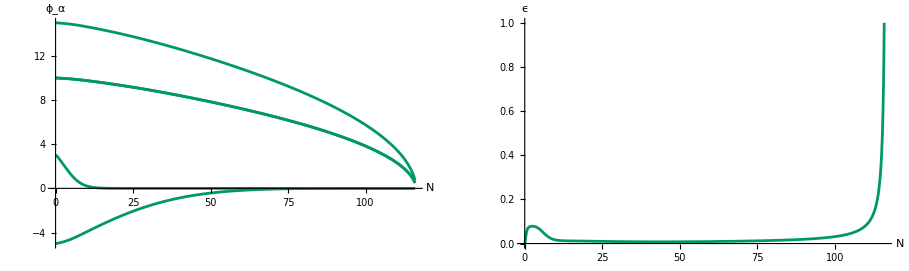

```mathematica
GraphicsRow[
{Plot[ϕα/.backgroundsol,{t,0,Nend},LabelStyle->Labels,PlotStyle->Green2,AxesLabel->{"N","ϕ_α"}],Plot[ϵ/.backgroundsol,{t,0,Nend},LabelStyle->Labels,PlotStyle->Green2,AxesLabel->{"N","ϵ"},PlotRange->All]}
]
Which[
d==2,Print[ParametricPlot[ϕα/.backgroundsol,{t,0,Nend},LabelStyle->Labels,PlotStyle->Green2,AspectRatio->1/GoldenRatio,AxesLabel->{"ϕ1","ϕ2"},PlotRange->All]],
d==3,Print[ParametricPlot3D[ϕα/.s,{t,Nstart,Nend},LabelStyle->Labels,PlotStyle->Green2,AspectRatio->1/GoldenRatio,AxesLabel->{"ϕ1","ϕ2","ϕ3"},PlotRange->All]]
]
```

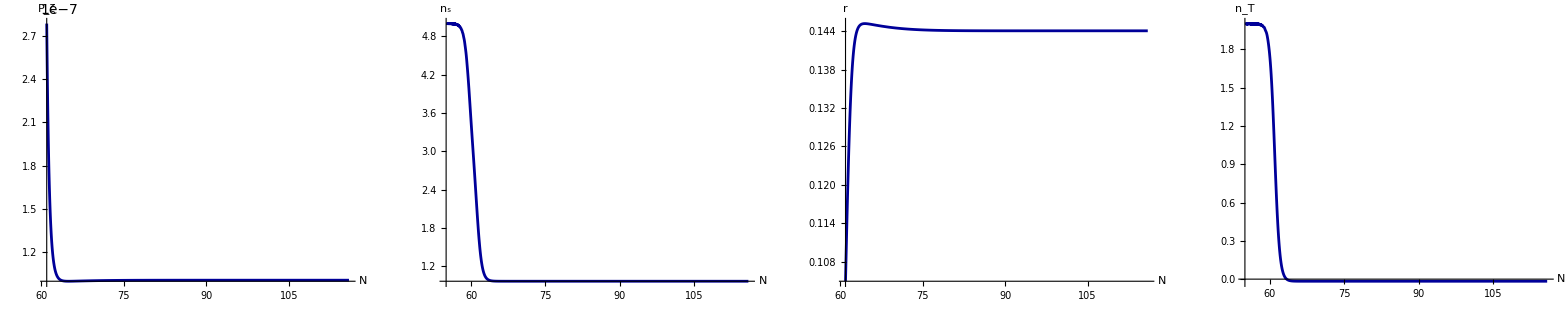

```mathematica
GraphicsRow[{
Plot[Evaluate[P/.s],{t,Nexit,Nend},LabelStyle->Labels,PlotStyle->Blue1,PlotRange->All,AxesLabel->{"N","P_ζ"}],
Plot[Evaluate[ns/.s],{t,Nstart,Nend},LabelStyle->Labels,PlotStyle->Blue1,PlotRange->All,AxesLabel->{"N","n_s"}],
Plot[Evaluate[r/.s],{t,Nexit,Nend},LabelStyle->Labels,PlotStyle->Blue1,PlotRange->All,AxesLabel->{"N","r"}],
Plot[Evaluate[nT/.s],{t,Nstart,Nend},LabelStyle->Labels,PlotStyle->Blue1,PlotRange->All,AxesLabel->{"N","n_T"}]
}]
```

Plotting the eigenvalues of the expansion tensor can take a long time and may not be necessary. As such this plot has been time constrained.

```mathematica
timeconstraint=10;
TimeConstrained[Plot[Eigenvalues[uαβSR/.s],{t,Nexit,Nend},LabelStyle->Labels,PlotStyle->{Green2},AxesLabel->{"N","λ"}],timeconstraint]
```

$Aborted

## Finite difference computation of spectral index and running

Time to compute perturbations = 5.47556

n_s = 0.963304 α = -0.000189014 r = 0.144033 P_ζ = 1.00755×10^-7

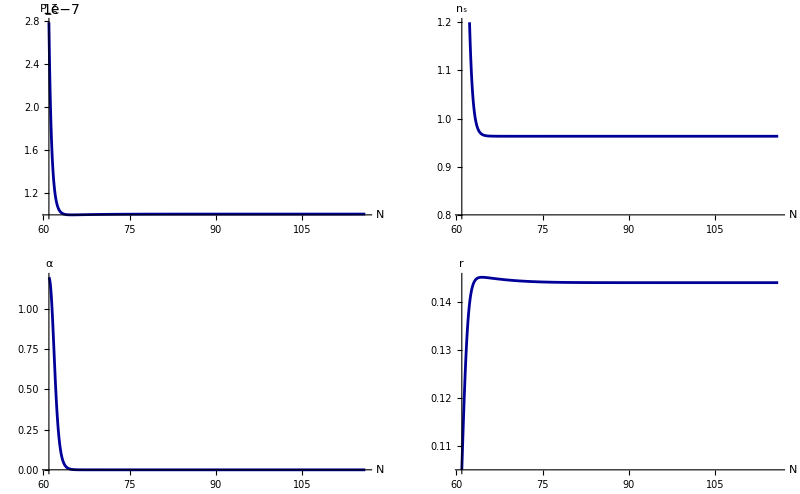

```mathematica
If[ComputensFiniteDifference,
Clear[Nexit,Nstart,ϕstart,πstart,ϕstartIC,πstartIC];
SetSharedFunction[sf];
SetSharedVariable[kList];
kList={};

Npivot=Nend-NexittoNend;
Nstartpivot=Nend-NexittoNend-Nsubhorizon;
Hpivot=First[H/.backgroundsol/.t->Npivot];

Hstart=First[H/.backgroundsol/.t->Nstart];
γinvstart=First[γinv/.backgroundsol/.t->Nstart];
ϕstart=First[ϕα/.backgroundsol/.t->Nstart];
πstart=First[πα/.backgroundsol/.t->Nstart];
ϕstartIC= Thread[(ϕα /. t -> Nstart) ==ϕstart];
πstartIC= Thread[(πα /. t -> Nstart) ==πstart];
Hexit=First[H/.backgroundsol/.t->Nexit];

finiteksteps =3;(*finite difference is computed using three points*)
Print["Time to compute perturbations = ",First@AbsoluteTiming[

ParallelDo[

Nstart=Nstartpivot-1+i/2;
Nexit=Npivot-1+i/2;

sf[i]=NDSolve[eqlistloop,paramsloop,{t,Nstart,Nend},AccuracyGoal->13,MaxSteps->Infinity,Method->{"EquationSimplification"->"Solve"}];

AppendTo[kList,{i,Hexit ⅇ^Nexit}]

,{i,finiteksteps}]
]];

sortedkList=Sort[kList];

P1=Na.Σab.Na/.sf[1];
P2=Na.Σab.Na/.sf[2];
P3=Na.Σab.Na/.sf[3];

r2=(4 Γab[[1,1]]/.sf[2])/P2;

nFD=(Log[P3]-Log[P1])/(Log[sortedkList[[3,2]]]-Log[sortedkList[[1,2]]])+1;

αFD=((Log[P3]-Log[P2])/(Log[sortedkList[[3,2]]]-Log[sortedkList[[2,2]]])-(Log[P2]-Log[P1])/(Log[sortedkList[[2,2]]]-Log[sortedkList[[1,2]]]))/(1/2(Log[sortedkList[[3,2]]]+Log[sortedkList[[2,2]]])-1/2(Log[sortedkList[[2,2]]]+Log[sortedkList[[1,2]]]));

Print["n_s = ",First[nFD/.t->Nend]," α = ",First[αFD/.t->Nend]," r = ",First[r2/.t->Nend]," P_ζ = ",First[P2/.t->Nend]];

Print@GraphicsGrid[{{
Plot[P2,{t,Npivot,Nend},LabelStyle->Labels,PlotStyle->Blue1,PlotRange->All,AxesLabel->{"N","P_ζ"}],
Plot[nFD,{t,Npivot,Nend},LabelStyle->Labels,PlotStyle->Blue1,AxesLabel->{"N","n_s"},PlotRange->{{Npivot,Nend},{0.8,1.2}}]},{
Plot[αFD,{t,Npivot,Nend},LabelStyle->Labels,PlotStyle->Blue1,PlotRange->All,AxesLabel->{"N","α"}],
Plot[r2,{t,Npivot,Nend},LabelStyle->Labels,PlotStyle->Blue1,PlotRange->All,AxesLabel->{"N","r"}]
}}]
,Print["Finite difference calculation of spectral index and runnning is not activated"]]
```

## P_ζ(k)

Time to compute perturbations = 486.127

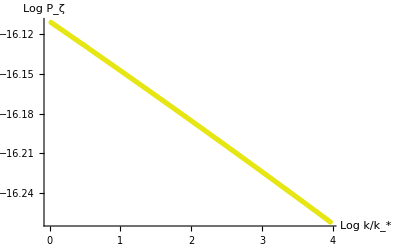

```mathematica
If[ComputePofk,
Clear[Nexit,Nstart,ϕstart,πstart,ϕstartIC,πstartIC];
SetSharedVariable[ΣList];
ΣList={};

Npivot=Nend-NexittoNend;
Nstartpivot=Nend-NexittoNend-Nsubhorizon;
Hpivot=First[H/.backgroundsol/.t->Npivot];

Hstart=First[H/.backgroundsol/.t->Nstart];
γinvstart=First[γinv/.backgroundsol/.t->Nstart];
ϕstart=First[ϕα/.backgroundsol/.t->Nstart];
πstart=First[πα/.backgroundsol/.t->Nstart];
ϕstartIC= Thread[(ϕα /. t -> Nstart) ==ϕstart];
πstartIC= Thread[(πα /. t -> Nstart) ==πstart];
Hexit=First[H/.backgroundsol/.t->Nexit];
Nexits={};
Print["Time to compute perturbations = ",First@AbsoluteTiming[
Do[

Nstart=Nstartpivot+(Nrange i)/ksteps;
Nexit=Npivot+(Nrange i)/ksteps;
AppendTo[Nexits,Nexit];

sk=NDSolve[eqlistloop,paramsloop,{t,Nstart,Nend},AccuracyGoal->13,MaxSteps->Infinity,Method->{"EquationSimplification"->"Solve"}];
AppendTo[ΣList,{Log[Hexit ⅇ^Nexit],First[Σab/.sk/.t->Nend]}];

,{i,ksteps}]

]];
NaNend=First[Na/.backgroundsol/.t->Nend];

Pk=Table[{ΣList[[l,1]]-Log[Hpivot ⅇ^Npivot],Log[First[(Na/.backgroundsol/.t->Nend)].ΣList[[l,2]].First[(Na/.backgroundsol/.t->Nend)]]},{l,ksteps}];
Print[Show[ListLinePlot[Sort[Pk],PlotStyle->Blue1,LabelStyle->Labels,AxesLabel->{"Log k/k_*","Log P_ζ"}],ListPlot[Pk,PlotStyle->Green1]]];

,Print["P_ζ(k) calculation not activated"]]
```

```mathematica
Nend
```

115.953

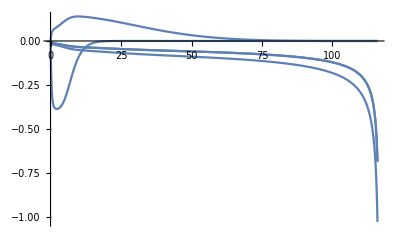

```mathematica
Plot[πα/.backgroundsol/.t-> n,{n,0,Nend},PlotRange->All]
```

```mathematica
πα/.backgroundsol/.t-> Npivot
```

{{-0.0981672,-0.0654448,0.0155938,-0.0654448,1.0279×10^-21}}

```mathematica
Npivot
```

60.9528

```mathematica
NaNend
```

{0.720872,0.480581,-3.28069×10^-10,0.480581,1.11997×10^-42,-0.257248,-0.171499,-2.38094×10^-11,-0.171499,-2.59064×10^-44}

```mathematica
NaNend2 = First[Join[-1/(2 ϵ)πα ,ConstantArray[0,d]] /.backgroundsol/.t-> Nend]
```

{0.514496,0.342997,4.76188×10^-11,0.342997,5.18127×10^-44,0,0,0,0,0}

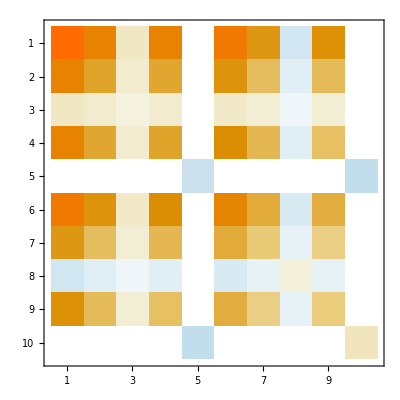

```mathematica
ΣList[[1,2]] // MatrixPlot
```

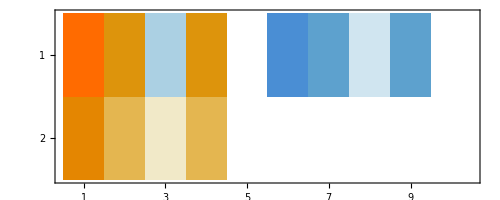

```mathematica
{NaNend,NaNend2} // MatrixPlot
```

```mathematica
NaNend.ΣList[[1,2]].NaNend - NaNend2.ΣList[[1,2]].NaNend2
```

-7.01685×10^-14

```mathematica
Speak["All calculations completed"]
```

```mathematica
NaNend.ΣList[[1,2]].NaNend
```

1.00681×10^-7

```mathematica
Eigenvalues[ΣList[[1,2]]]
```

{3.30959×10^-7,2.48031×10^-11,2.48031×10^-11,9.31788×10^-13,4.75516×10^-14,-4.75206×10^-15,2.08136×10^-18,2.0813×10^-18,-3.06955×10^-27,4.95442×10^-28}

```mathematica
Norm[NaNend2]
```

0.707107

```mathematica
1/Norm[D[ϕα,t]] /. backgroundsol /.t-> Nend
```

{0.707107}

```mathematica
NaNend2
```

{0.514496,0.342997,4.76188×10^-11,0.342997,5.18127×10^-44,0,0,0,0,0}

## Isocurvature Perturbations

```mathematica
(*vialpha = onframe(gNe4[:Nf])*)
OnFrame[vec_]:= Module[{a,c,dumbBasis},
 c = Length[vec];
a = Position[vec,_?(#≠0&),1,1]⟦1,1⟧; (* first nonzero element *)
dumbBasis = Join[{vec},IdentityMatrix[c]⟦;;a-1⟧,IdentityMatrix[c]⟦a+1;;⟧];
(DeleteCases[#,ConstantArray[0,Length@#[[1]]]]&@Orthogonalize[dumbBasis])[[2;;]]
];
```

```mathematica
(* Python line: 
p['Pz_trans_iso'].append((p['hs'][eend]/np.linalg.norm(p['fs'][eend]))**2*np.einsum('ia,ab,ib->',vialpha,Send[:Nf,:Nf],vialpha)/(2*np.pi**2)) *)

via = OnFrame[First[-1/(2 ϵ)πα /.backgroundsol/.t-> Nend]];
Piso=1/(2 π^2)(1/Norm[πα])^2 Tr[via . ΣList[[1,2,;;d,;;d]] . Transpose[via]] /.backgroundsol/.t-> Nend
```

{4.24006×10^-13}

```mathematica
via
```

{{-0.403604,0.874475,-3.73553×10^-11,-0.269069,-4.06453×10^-44},{-6.40761×10^-11,6.01601×10^-28,1.,-4.27174×10^-11,-6.45284×10^-54},{-0.5547,-5.76296×10^-17,-5.42553×10^-27,0.83205,-5.58616×10^-44},{-1.00706×10^-43,-2.33971×10^-60,3.02633×10^-70,-7.84155×10^-60,1.}}

```mathematica
((1/Norm[πα])^2 /.backgroundsol/.t-> Nend)
```

{0.5}

```mathematica
Tr[via.ΣList[[1,2,;;d,;;d]].Transpose[via] /.backgroundsol/.t-> Nend]
```

8.37054×10^-12

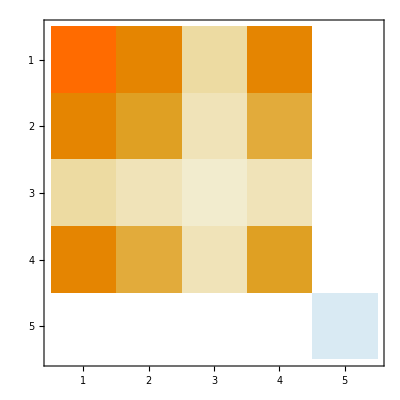

```mathematica
ΣList⟦1,2,;;d,;;d⟧ // MatrixPlot
```

```mathematica
H /.backgroundsol/.t-> Nend
```

{5.04671×10^-6}

```mathematica
pythonΣList12={{1.34176321*^-07,8.94449753*^-08 ,3.00870437*^-17, 8.94449753*^-08 ,2.10294144*^-32},{8.94449753*^-08 ,5.96388418*^-08 ,2.00580291*^-17, 5.96299835*^-08 ,1.40196096*^-32},{3.00870437*^-17, 2.00580291*^-17 ,7.36641690*^-27, 2.00580291*^-17, 4.80308839*^-42},{8.94449753*^-08, 5.96299835*^-08 ,2.00580291*^-17 ,5.96388418*^-08 ,1.40196096*^-32},{2.10294144*^-32 ,1.40196096*^-32 ,4.80308839*^-42 ,1.40196096*^-32, 2.38321483*^-15}}
```

{{1.34176×10^-7,8.9445×10^-8,3.0087×10^-17,8.9445×10^-8,2.10294×10^-32},{8.9445×10^-8,5.96388×10^-8,2.0058×10^-17,5.963×10^-8,1.40196×10^-32},{3.0087×10^-17,2.0058×10^-17,7.36642×10^-27,2.0058×10^-17,4.80309×10^-42},{8.9445×10^-8,5.963×10^-8,2.0058×10^-17,5.96388×10^-8,1.40196×10^-32},{2.10294×10^-32,1.40196×10^-32,4.80309×10^-42,1.40196×10^-32,2.38321×10^-15}}

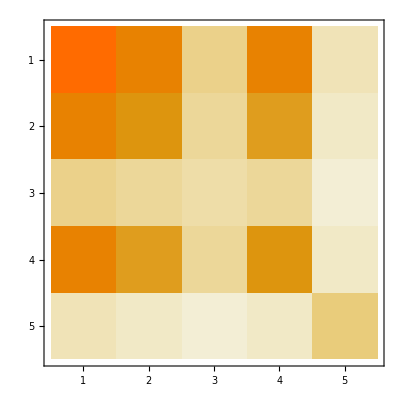
{-Graphics-,-Graphics-}

```mathematica
MatrixPlot/@{ΣList⟦1,2,;;d,;;d⟧,pythonΣList12 }
```

```mathematica
ΣList⟦1,2,;;d,;;d⟧⟦5,5⟧
```

-1.9892×10^-15

```mathematica
pythonΣList12⟦5,5⟧
```

2.38321×10^-15